```mathematica
(*Import data*)

SetDirectory[NotebookDirectory[]]
data=Import["matrix_vs_t(6).dat"];
dimx=50;
dimy=50;
Length[data];
Lent=Round[Length[data]/dimx];
f3[x_,y_,z_]:=0
t=1;Mat=Array[f3,{Lent+1,dimx,dimy}];
For[i=1,i≤Length[data],i++,
For[j=1,j≤dimy,j++,
i1=Mod[i,dimx];
If[Mod[i,dimx]==0,i1=dimx];
Mat[[t]][[i1]][[j]]=data[[i]][[j]];
];If[Mod[i,dimx]==0,t=t+1;]
]
```

C:\Users\adity\OneDrive - Imperial College London\Freelancing\Hoffman Evolutionary Games

```mathematica
(*Movie of matrix vs time*)
Manipulate[MatrixPlot[Mat[[c]],ColorRules->{0->White,0.25->Green,0.5->Black,1->Red}],{c,1,Lent,1}]
```

```mathematica
(*Exporting movie*)
frame[t_]:=MatrixPlot[Mat[[t]],ColorRules->{0->White,0.25->Green,0.5->Black,1->Red}];
frames= Table[frame[t],{t,1,Lent,2}];
Export["population.avi",frames,"FrameRate"->1]
```

```mathematica
Export["population.avi",frames,"FrameRate"->5]
```

population.avi

```mathematica
Export["population.avi",frames,"FrameRate"->1]
```

population.avi

C:\Users\adity\OneDrive - Imperial College London\Freelancing\Hoffman Evolutionary Games

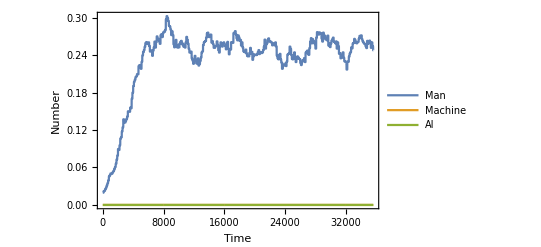

```mathematica
(*Import density plot vs time*)
SetDirectory[NotebookDirectory[]]
data=Import["density_vs_t.dat"];
ListPlot[{MovingAverage[data[[1;;,{1,2}]],10],MovingAverage[data[[1;;,{1,3}]],10],MovingAverage[data[[1;;,{1,4}]],10]},Joined->True,PlotLegends->{"Man","Machine","AI"},Frame->True,LabelStyle->FontSize[30],FrameLabel->{"Time","Number"},FrameStyle->Directive[14],PlotRange->All]
```

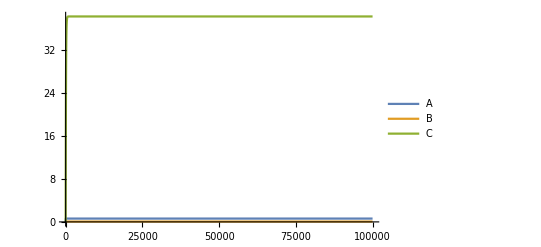

```mathematica
(*Plot differential equation (mean-field) to compare*)
Clear[A,B,CC,y,t];k1=1;k2=1;k3=1;k4=10;k5=0.01;
k6=10;
sol=NDSolve[{A'[t]==k1-k2*A[t]-k4*A[t]*B[t],B'[t]==k3*A[t]*A[t]-k4*A[t]*B[t],CC'[t]==k4*A[t]*B[t]-k5*CC[t],{A[0]==0,B[0]==0,CC[0]==0}},{A,B,CC},{t,0,100000}];
Plot[{A[t]/.sol,B[t]/.sol,CC[t]/.sol},{t,0,100000},PlotRange->All,PlotLegends->{"A","B","C"}]
```

```mathematica
Clear[A,B,CC]
Ao=1;
sol=NDSolve[{A'[t]==k1-k2*A[t]-k4*A[t]*B[t]+k6*(Ao-A[t]),B'[t]==k3*A[t]*A[t]-k4*A[t]*B[t]+k6*(Ao-A[t]),{A[0]==0,B[0]==0}},{A,B},{t,0,100}];
Plot[{A[t]/.sol,B[t]/.sol},{t,0,100},PlotRange->All,PlotLegends->{"A","B"}]
```